```mathematica
Quiet[ DeleteDirectory[ "FitExamples", DeleteContents -> True ], DeleteDirectory::nodir ];
Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
TestReport @ FileNameJoin @ { NotebookDirectory[ ], "Tests.wlt" }
```

### Basic Examples

Download some example fit files from the Fit SDK:

```mathematica
ExtractArchive["https://developer.garmin.com/downloads/fit/sdk/FitSDKRelease_21.94.00.zip","FitExamples","*/Activity.fit"]
```

{FitExamples\examples\Activity.fit,FitExamples\js\test\data\Activity.fit}

Import one of the files:

```mathematica
FITImport["FitExamples/examples/Activity.fit"]
```

Export a sample fit file corresponding to a bike ride:

```mathematica
Export["BikeRide.fit",ByteArray[…],"Binary"];
```

Import the file as a Dataset:

```mathematica
FITImport["BikeRide.fit"]
```

-Graphics-

Plot altitude over time:

```mathematica
DateListPlot[FITImport["BikeRide.fit","Altitude"]]
```

-Graphics-

View a map of a ride:

```mathematica
GeoGraphics[{Red,Thick,Line[Values[FITImport["BikeRide.fit","GeoPosition"]]]}]
```

-Graphics-

### Scope

### Options

#### FunctionalThresholdPower

Some values are not available without specifying an FTP value:

```mathematica
FITImport["BikeRide.fit","PowerZone"]
```

Missing[NotAvailable]

Specify an FTP when importing to get power zone data:

```mathematica
FITImport["BikeRide.fit","PowerZone","FunctionalThresholdPower"->Quantity[283,"Watts"]]
```

TimeSeries[…]

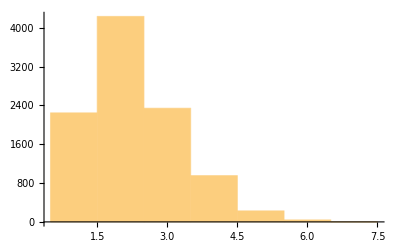

```mathematica
Histogram[Values[%]]
```

See how the distribution changes with different FTP values:

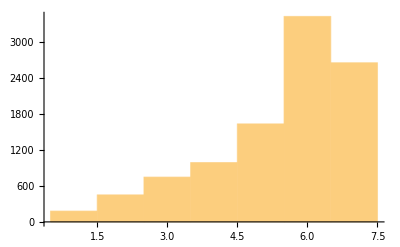
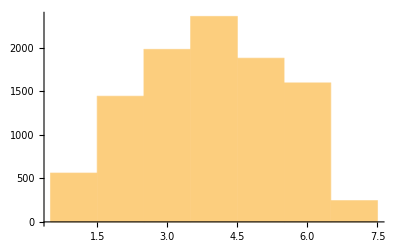
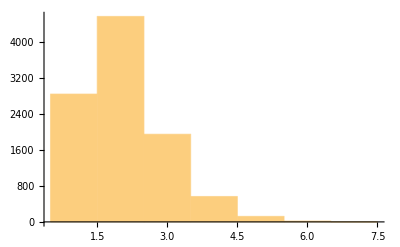

```mathematica
Histogram[Values[FITImport["BikeRide.fit","PowerZone","FunctionalThresholdPower"->Quantity[#,"Watts"]]]]&/@{150,200,300}
```

Set the FTP persistently:

```mathematica
PersistentSymbol["FITImport/FunctionalThresholdPower"]=Quantity[283,"Watts"]
```

283 W

Specifying the FunctionalThresholdPower option is no longer necessary:

```mathematica
FITImport["BikeRide.fit","PowerZone"]
```

TimeSeries[…]

Remove the stored value:

```mathematica
PersistentSymbol["FITImport/FunctionalThresholdPower"]=.
```

#### MaxHeartRate

Some values are not available without specifying a maximum heart rate:

```mathematica
FITImport["BikeRide.fit","HeartRateZone"]
```

Missing[NotAvailable]

Specify a max heart rate when importing to get HR zone data:

```mathematica
FITImport["BikeRide.fit","HeartRateZone","MaxHeartRate"->190]
```

TimeSeries[…]

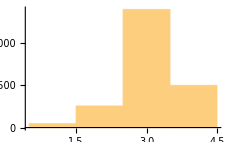

```mathematica
Histogram[Values[%]]
```

Set the max heart rate persistently:

```mathematica
PersistentSymbol["FITImport/MaxHeartRate"]=Quantity[190,"BPM"]
```

190 beats/min

Specifying the MaxHeartRate option is no longer necessary:

```mathematica
FITImport["BikeRide.fit","HeartRateZone"]
```

TimeSeries[…]

Remove the stored value:

```mathematica
PersistentSymbol["FITImport/MaxHeartRate"]=.
```

#### UnitSystem

By default, units are determined by the current value of $UnitSystem:

```mathematica
$UnitSystem
```

Imperial

```mathematica
FITImport["BikeRide.fit","Altitude"]["LastValue"]
```

2591.21 ft

Override the default unit system:

```mathematica
FITImport["BikeRide.fit","Altitude",UnitSystem->"Metric"]["LastValue"]
```

789.8 m

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

Animate a bike ride:

```mathematica
alt=Values[FITImport["BikeRide.fit","Altitude"]][[;;;;10]];
pos=Values[FITImport["BikeRide.fit","GeoPosition"]][[;;;;10]];
bounds=GeoBoundingBox[pos];
Animate[{
GeoGraphics[{Thick,Red,Line[Take[pos,n]]},GeoRange->bounds],
Show[ListLinePlot[alt],ListLinePlot[Take[alt,n],Filling->Bottom]]
},{n,1,Length[pos],1},DefaultDuration->30]
```

-Graphics-

Plot all the values found in a fit file:

```mathematica
Multicolumn[KeyValueMap[DateListPlot[#2,PlotLabel->#1]&,KeyDrop[FITImport["BikeRide.fit",All],{"Timestamp","GeoPosition"}]],3]
```

-Graphics-

Animate a Zwift ride:

```mathematica
Export["ZwiftRide.fit",ByteArray[…],"Binary"]
```

ZwiftRide.fit

```mathematica
pos=Reverse/@Values[FITImport["ZwiftRide.fit","GeoPosition"]][[All,1]];
watopia=ImageResize[First@Import["https://zwiftinsider.com/wp-content/uploads/2022/09/Watopia-2.15.pdf"],500];
Animate[
ImageCompose[Show[watopia,ImageSize->500],Graphics[{Thickness[.01],Yellow,Line[Take[pos,n]],Green,Disk[pos[[n]],0.0005]},],Scaled[{0.2746,0.3286}]],
{n,1,Length[pos],1},
DefaultDuration->30
]
```

-Graphics-